```mathematica
σ[r_]=Integrate[x*(UnitStep[x-1]+Log[x]*DiracDelta[x-1]-1),{x,0.001,r}];
```

```mathematica
σ[2]
```

-0.5

```mathematica
Integrate[x*(HeavisideTheta[x-1]+Log[x]*DiracDelta[x-1]-1),{x,0,r},Assumptions->r>0]
```

ConditionalExpression[-1/2,r>1]

```mathematica
Integrate[x*Log[x]*DiracDelta[x-1],{x,0,r},Assumptions->r>0]
```

0

```mathematica
σ[x_]=Integrate[x*(HeavisideTheta[x-1]+Log[x]*DiracDelta[x-1]-1),x];
```

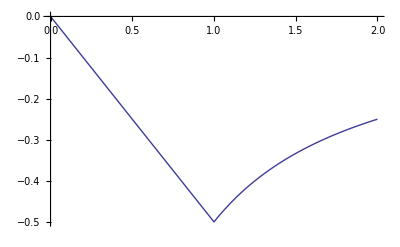

```mathematica
Plot[σ[x]/x,{x,0,2}]
```

```mathematica
Log[1]
```

0

```mathematica
Integrate[1/r*(HeavisideTheta[r-rs]),r]
```

HeavisideTheta[r-rs] (Log[r]-Log[rs])

```mathematica
Integrate[(1/x)*DiracDelta[x-r],x]
```

HeavisideTheta[-r+x]/r

```mathematica
Integrate[HeavisideTheta[-1+x],x]
```

(-1+x) HeavisideTheta[-1+x]

```mathematica
HeavisideTheta[0.0]
```

HeavisideTheta[0.]